```mathematica
s0 = ({{1, 0}, {0, 1}});
sx = ({{0, 1}, {1, 0}});
sy = ({{0, -ⅈ}, {ⅈ, 0}});
sz=({{1, 0}, {0, -1}});
```

```mathematica
I0[L_]:=Block[{xtp,ltp,i},
ltp = Table[s0,{i,1,L}];
xtp = ltp[[1]];
For[i=2,i≤L,i++,
xtp=KroneckerProduct[ltp[[i]],xtp];
];

xtp
];
```

```mathematica
X[l_,L_]:=Block[{xtp,ltp,i},
ltp = Table[s0,{i,1,L}];
ltp[[l]]=x;
xtp = ltp[[1]];
For[i=2,i≤L,i++,
xtp=KroneckerProduct[ltp[[i]],xtp];
];

xtp
];

Y[l_,L_]:=Block[{xtp,ltp,i},
ltp = Table[s0,{i,1,L}];
ltp[[l]]=y;
xtp = ltp[[1]];
For[i=2,i≤L,i++,
xtp=KroneckerProduct[ltp[[i]],xtp];
];

xtp
];

Z[l_,L_]:=Block[{xtp,ltp,i},
ltp = Table[s0,{i,1,L}];
ltp[[l]]=z;
xtp = ltp[[1]];
For[i=2,i≤L,i++,
xtp=KroneckerProduct[ltp[[i]],xtp];
];

xtp
];
```

```mathematica
Rzx[i_,j_,ϕ_]:=Cos[ϕ]I0[3]+ⅈ Sin[ϕ]Z[i,3].X[j,3];
```

```mathematica
Rzx[1,2,ϕ]//MatrixForm
```

(Cos[ϕ] | 0 | ⅈ Sin[ϕ] | 0 | 0 | 0 | 0 | 0
0 | Cos[ϕ] | 0 | -ⅈ Sin[ϕ] | 0 | 0 | 0 | 0
ⅈ Sin[ϕ] | 0 | Cos[ϕ] | 0 | 0 | 0 | 0 | 0
0 | -ⅈ Sin[ϕ] | 0 | Cos[ϕ] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Cos[ϕ] | 0 | ⅈ Sin[ϕ] | 0
0 | 0 | 0 | 0 | 0 | Cos[ϕ] | 0 | -ⅈ Sin[ϕ]
0 | 0 | 0 | 0 | ⅈ Sin[ϕ] | 0 | Cos[ϕ] | 0
0 | 0 | 0 | 0 | 0 | -ⅈ Sin[ϕ] | 0 | Cos[ϕ])

```mathematica
Cos[ϕ]^2 I0[3]+ⅈ Sin[ϕ]^2 Z[1,3].Y[2,3].X[3,3]+ⅈ Cos[ϕ]Sin[ϕ](Z[1,3].X[2,3]+Z[2,3].X[3,3])-Rzx[1,2,ϕ].Rzx[2,3,ϕ]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(Cos[ϕ]I0[3]-ⅈ Sin[ϕ]Z[2,3].X[3,3]).(Cos[ϕ]^2 I0[3]+ⅈ Sin[ϕ]^2 Z[1,3].Y[2,3].X[3,3]+ⅈ Cos[ϕ]Sin[ϕ](Z[1,3].X[2,3]+Z[2,3].X[3,3]))-Rzx[2,3,-ϕ].Rzx[1,2,ϕ].Rzx[2,3,ϕ]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Simplify[Cos[ϕ]I0[3]+2ⅈ Cos[ϕ] Sin[ϕ]^2 Z[1,3].Y[2,3].X[3,3]+ⅈ Cos[2ϕ]Sin[ϕ]Z[1,3].X[2,3]-Rzx[2,3,-ϕ].Rzx[1,2,ϕ].Rzx[2,3,ϕ]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(****)
```

```mathematica
Simplify[(Cos[ϕ]I0[3]+2ⅈ Cos[ϕ] Sin[ϕ]^2 Z[1,3].Y[2,3].X[3,3]+ⅈ Cos[2ϕ]Sin[ϕ]Z[1,3].X[2,3]).(Cos[θ]I0[3]-ⅈ Sin[θ] Z[1,3].X[2,3])-Rzx[2,3,-ϕ].Rzx[1,2,ϕ].Rzx[2,3,ϕ].Rzx[1,2,-θ]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Simplify[(Cos[θ]Cos[ϕ]+ Sin[θ]  Cos[2ϕ]Sin[ϕ])I0[3]+ⅈ (Cos[θ]Cos[2ϕ]Sin[ϕ]-Sin[θ] Cos[ϕ])Z[1,3].X[2,3]-ⅈ 2 Sin[θ]  Cos[ϕ] Sin[ϕ]^2 Z[2,3].X[3,3]+2ⅈ Cos[θ] Cos[ϕ] Sin[ϕ]^2 Z[1,3].Y[2,3].X[3,3]-Rzx[2,3,-ϕ].Rzx[1,2,ϕ].Rzx[2,3,ϕ].Rzx[1,2,-θ]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(**Try again**)
```

```mathematica
Cos[ϕ]^2 I0[3]+ⅈ Sin[ϕ]^2 Z[1,3].Y[2,3].X[3,3]+ⅈ Cos[ϕ]Sin[ϕ](Z[1,3].X[2,3]+Z[2,3].X[3,3])-Rzx[1,2,ϕ].Rzx[2,3,ϕ]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Cos[ϕ]^2 I0[3]+ⅈ Sin[ϕ]^2 Z[1,3].Y[2,3].X[3,3]-ⅈ Cos[ϕ]Sin[ϕ](Z[1,3].X[2,3]+Z[2,3].X[3,3])-Rzx[1,2,-ϕ].Rzx[2,3,-ϕ]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Simplify[(Cos[ϕ]^2 I0[3]+ⅈ Sin[ϕ]^2 Z[1,3].Y[2,3].X[3,3]+ⅈ Cos[ϕ]Sin[ϕ](Z[1,3].X[2,3]+Z[2,3].X[3,3])).(Cos[θ]^2 I0[3]+ⅈ Sin[θ]^2 Z[1,3].Y[2,3].X[3,3]-ⅈ Cos[θ]Sin[θ](Z[1,3].X[2,3]+Z[2,3].X[3,3]))-Rzx[1,2,ϕ].Rzx[2,3,ϕ].Rzx[1,2,-θ].Rzx[2,3,-θ]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Simplify[Cos[θ]^2 Cos[ϕ]^2 I0[3]+ⅈ Sin[θ]^2 Cos[ϕ]^2 Z[1,3].Y[2,3].X[3,3]-ⅈ Cos[θ]Sin[θ] Cos[ϕ]^2(Z[1,3].X[2,3]+Z[2,3].X[3,3])+ⅈ Cos[θ]^2 Sin[ϕ]^2 Z[1,3].Y[2,3].X[3,3]- Sin[θ]^2 Sin[ϕ]^2 I0[3]+ Cos[θ]Sin[θ]ⅈ Sin[ϕ]^2(- Z[2,3].X[3,3]+Z[1,3].X[2,3])+(ⅈ Cos[θ]^2 Cos[ϕ]Sin[ϕ](Z[1,3].X[2,3]+Z[2,3].X[3,3])+ⅈ Sin[θ]^2 ⅈ Cos[ϕ]Sin[ϕ](ⅈ Z[2,3].X[3,3]-ⅈ Z[1,3].X[2,3])+2 Cos[θ]Sin[θ] Cos[ϕ]Sin[ϕ]I0[3])-Rzx[1,2,ϕ].Rzx[2,3,ϕ].Rzx[1,2,-θ].Rzx[2,3,-θ]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Simplify[(Cos[θ]^2 Cos[ϕ]^2+2 Cos[θ]Sin[θ] Cos[ϕ]Sin[ϕ]- Sin[θ]^2 Sin[ϕ]^2)I0[3]+ⅈ (Sin[θ]^2 Cos[ϕ]^2+Cos[θ]^2 Sin[ϕ]^2)Z[1,3].Y[2,3].X[3,3]+ⅈ(- Cos[θ]Sin[θ] Cos[ϕ]^2+Cos[θ]Sin[θ] Sin[ϕ]^2+ Cos[θ]^2 Cos[ϕ]Sin[ϕ]+ Sin[θ]^2 Cos[ϕ]Sin[ϕ])Z[1,3].X[2,3]+ⅈ (-Cos[θ]Sin[θ] Cos[ϕ]^2-Cos[θ]Sin[θ] Sin[ϕ]^2+Cos[θ]^2 Cos[ϕ]Sin[ϕ]-Sin[θ]^2 Cos[ϕ]Sin[ϕ])(Z[2,3].X[3,3])-Rzx[1,2,ϕ].Rzx[2,3,ϕ].Rzx[1,2,-θ].Rzx[2,3,-θ]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
A[θ_,ϕ_]:=(- Cos[θ]Sin[θ] Cos[ϕ]^2+Cos[θ]Sin[θ] Sin[ϕ]^2+ Cos[θ]^2 Cos[ϕ]Sin[ϕ]+ Sin[θ]^2 Cos[ϕ]Sin[ϕ]);
B[θ_,ϕ_]:=(-Cos[θ]Sin[θ] Cos[ϕ]^2-Cos[θ]Sin[θ] Sin[ϕ]^2+Cos[θ]^2 Cos[ϕ]Sin[ϕ]-Sin[θ]^2 Cos[ϕ]Sin[ϕ])
```

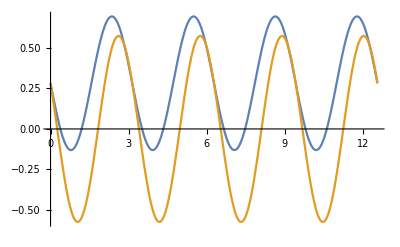

```mathematica
Plot[{A[θ,0.3],B[θ,0.3]},{θ,0,4π}]
```

```mathematica
(*Try again*)
```

```mathematica
Cos[ϕ]Cos[θ]I0[3]+ⅈ Sin[ϕ]Sin[θ]Z[1,3].Y[2,3].X[3,3]+ⅈ (Cos[θ]Sin[ϕ]Z[1,3].X[2,3]+Cos[ϕ]Sin[θ]Z[2,3].X[3,3])-Rzx[1,2,ϕ].Rzx[2,3,θ]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Simplify[(Cos[ϕ]Cos[θ]I0[3]+ⅈ Sin[ϕ]Sin[θ]Z[1,3].Y[2,3].X[3,3]+ⅈ (Cos[θ]Sin[ϕ]Z[1,3].X[2,3]+Cos[ϕ]Sin[θ]Z[2,3].X[3,3])).(Cos[λ]I0[3]+ⅈ Sin[λ]Z[1,3].X[2,3])-Rzx[1,2,ϕ].Rzx[2,3,θ].Rzx[1,2,λ]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Simplify[(Cos[λ]Cos[ϕ]Cos[θ]I0[3]+ⅈ Sin[λ]Cos[ϕ]Cos[θ]Z[1,3].X[2,3])+(ⅈ Cos[λ] Sin[ϕ]Sin[θ]Z[1,3].Y[2,3].X[3,3]+ⅈ Sin[λ] Sin[ϕ]Sin[θ] Z[2,3].X[3,3])+  ⅈ Cos[λ]Cos[θ]Sin[ϕ]Z[1,3].X[2,3]+ ⅈ Cos[λ]Cos[ϕ]Sin[θ]Z[2,3].X[3,3]+-Sin[λ]Cos[θ]Sin[ϕ]I0[3]-ⅈ Sin[λ] Cos[ϕ]Sin[θ]Z[1,3].Y[2,3].X[3,3]-Rzx[1,2,ϕ].Rzx[2,3,θ].Rzx[1,2,λ]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Simplify[(Cos[λ]Cos[ϕ]Cos[θ]-Sin[λ]Cos[θ]Sin[ϕ])I0[3]+ⅈ (Cos[λ] Sin[ϕ]Sin[θ]-Sin[λ] Cos[ϕ]Sin[θ])Z[1,3].Y[2,3].X[3,3]+ⅈ (Sin[λ]Cos[ϕ]Cos[θ]+  Cos[λ]Cos[θ]Sin[ϕ])Z[1,3].X[2,3]+ⅈ (Sin[λ] Sin[ϕ]Sin[θ] +Cos[λ]Cos[ϕ]Sin[θ])Z[2,3].X[3,3]-Rzx[1,2,ϕ].Rzx[2,3,θ].Rzx[1,2,λ]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
λ = ArcTan[-(Sin[ϕ]Cos[θ])/(Cos[ϕ]Cos[θ])];
Simplify[(Sin[λ]Cos[ϕ]Cos[θ]+Cos[λ]Cos[θ]Sin[ϕ])]
```

0

```mathematica
ϕ=π/4;
Simplify[(Sin[λ]Sin[ϕ]Sin[θ]+Cos[λ]Cos[ϕ]Sin[θ])]
```

0

```mathematica
(Cos[λ] Sin[ϕ]Sin[θ]-Sin[λ] Cos[ϕ]Sin[θ])
```

Sin[θ]

```mathematica
(Cos[λ]Cos[ϕ]Cos[θ]-Sin[λ]Cos[θ]Sin[ϕ])
```

Cos[θ]

```mathematica
λ = ArcTan[-(Sin[ϕ]Cos[θ])/(Cos[ϕ]Cos[θ])]
```

-π/4

```mathematica
Simplify[(Cos[θ])I0[3]+ⅈ (Sin[θ])Z[1,3].Y[2,3].X[3,3]-Rzx[1,2,π/4].Rzx[2,3,θ].Rzx[1,2,-π/4]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*Is there a way to avoid the π/4?*)
```

```mathematica
Clear[ϕ]
λ = ArcTan[-Sin[ϕ]/Cos[ϕ]];
Simplify[(Sin[λ]Cos[ϕ]Cos[θ]+Cos[λ]Cos[θ]Sin[ϕ])]
```

0

```mathematica
Simplify[(Sin[λ]Sin[ϕ]Sin[θ]+Cos[λ]Cos[ϕ]Sin[θ])]
```

Cos[ϕ] Cos[2 ϕ] √(Sec[ϕ]^2) Sin[θ]